## Pre-Computing the BRDF Integral

We need to find a way to approximate the lighting integral for the specular part of our area light.
The integral writes as:

	L(ω_o)=∫_Ω L(ω_i) f_r(ω_o,ω_i)(ω_i.n)dω_i
	
Ω is the solid angle covered by the upper hemisphere above the surface.

We proceed in the same way as http://blog.selfshadow.com/publications/s2013-shading-course/karis/s2013_pbs_epic _notes _v2.pdf to separate the integral in several parts:

#### Splitting the integral

L(ω_o)≃ ∫_Ω L(ω_i,ρ) (ω_i.n) dω_i  ∫_Ω f_r(ω_o,ω_i)(ω_i.n)dω_i

∫_Ω L'(ω_i,ρ) (ω_i.n) dω_i  represents the pre-filtered source of radiance. It could be an env-map in the case of IBL, or our area light in this case.
∫_Ω f_r(ω_o,ω_i)(ω_i.n)dω_i represents the BRDF integral as if lit by a uniform source of radiance (L(ω_i)=1).

#### BRDF integral

Here, we’ re going to concentrate on the BRDF integral.
Assuming the BRDF f_r(ω_o,ω_i) is our Ward-Dür model, coupled with Fresnel, we obtain:

	L_brdf(ω_o)≃ ∫_Ω  F(ω_o,ω_i,n) D(ω_o,ω_i,n) (ω_i.n)dω_i

F(ω_o,ω_i,n) is the Fresnel term (note that we’ll use the Schlick' s fresnel approximation, not our complex fresnel otherwise the integral would be more difficult to separate).
D(ω_o,ω_i,n) is the Normal Distribution Function of the micro-facet model.
There is no masking/shadowing term as it is already accounted for by the Ward-Dür NDF.

Assuming the Schlick fresnel term is:

	F_schlick(ω_o,h)=F_0+(1-F_0)(1-ω_o.h)^5 = F_0 (1-(1-ω_o.h)^5) + (1-ω_o.h)^5 

We can further split the integral into 2 parts:

	L_brdf(ω_o)≃ F_0∫_Ω  (1-(1-ω_o.h)^5)D(ω_o,ω_i,n) (ω_i.n)dω_i + ∫_Ω  (1-ω_o.h)^5 D(ω_o,ω_i,n) (ω_i.n)dω_i

Ignoring anisotropy, we have:

	D(ω_o,ω_i,n,α) = ρ_s/πα^2 e^(-(tan^2 Θ_h)/α^2) 2(1+cos Θ_l cos Θ_v +sin Θ_l sin Θ_v cos( Φ_v-Φ_l))/(cos Θ_l + cos Θ_v)^4 

Or:
	D(ω_o,ω_i,n,α) = ρ_s/πα^2 e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4
	
and ĥ = ω_o +ω_i  (non-normalized!)
	
This gives us:

	L_brdf(ω_o,α)≃ ρ_s/πα^2[ F_0∫_Ω  (1-(1-ω_o.h)^5)e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4 (ω_i.n)dω_i + ∫_Ω  (1-ω_o.h)^5 e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4 (ω_i.n)dω_i]
	
	L_brdf(ω_o.n,α)≃ ρ_s/2[F_0 A(ω_o.n,α) +B(ω_o.n,α)]

Where:
	A(ω_o.n,α)= 1/α^2∫_0^(π/2)  (1-(1-ω_o.n)^5)e^(-(tan^2 Θ_h)/α^2)(ĥ.ĥ)/(ĥ.n)^4 sin Θ dΘ
	B(ω_o.n,α) = 1/α^2∫_0^(π/2)  (1-ω_o.n)^5 e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4 sin Θ dΘ

Both A and B are bounded in [0,1] because the integral of BRDF is ≤ 1, as shown by Dür in his paper.

#### WRONG! Light direction is NOT the reflected view direction! Now, in our special case, we also have the incoming (light) direction ω_i which is the reflection of the outgoing (view) direction: ω_i= 2(ω_o.n).n - ω_o or simply, in terms of angles, Θ_l=Θ_v and Φ_l=Φ_v+π h = (ω_i+ω_o)/(|ω_i+ω_o|)=(2(ω_o.n).n)/(2(ω_o.n))=n So D(ω_o,ω_i,n) further simplifies into: D(ω_o,ω_i,n) = ρ_s/πα^2 e^(-((tan Θ_h)/α^2)^2) 2(1+cos Θ_l cos Θ_v +sin Θ_l sin Θ_v cos( Φ_v-Φ_l))/(cos Θ_l + cos Θ_v)^4 = ρ_s/πα^2 2(1+cos^2 Θ_v -sin^2 Θ_v )/(2 cos Θ_v)^4=ρ_s/πα^2(4 cos^2 Θ_v)/(16 cos^4 Θ_v)=ρ_s/(4 πα^2 cos^2 Θ_v) And L_brdf(ω_o) becomes: L_brdf(ω_o.n,α)≃ ρ_s/(4π)[F_0∫_Ω (1-(1-ω_o.n)^5)1/(α^2(ω_o.n))dω_i +∫_Ω (1-ω_o.n)^5 1/(α^2(ω_o.n))dω_i] L_brdf(ω_o.n,α)≃ ρ_s/2[F_0∫_0^(π/2) (1-(1-ω_o.n)^5)1/(α^2(ω_o.n))sin Θ dΘ +∫_0^(π/2) (1-ω_o.n)^5 1/(α^2(ω_o.n))sin Θ dΘ] L_brdf(ω_o.n,α)≃ ρ_s/2[F_0 A(ω_o.n,α) +B(ω_o.n,α)] Where: A(ω_o.n,α)= ∫_0^(π/2) (1-(1-ω_o.n)^5)1/(α^2(ω_o.n))sin Θ dΘ B(ω_o.n,α) = ∫_0^(π/2) (1-ω_o.n)^5 1/(α^2(ω_o.n))sin Θ dΘ

### Plotting the 2 parts

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]; 
rawBRDFpart = BinaryReadList["./BRDF0_64x64.bin",{"Real32", "Real32"}]
```

{{0.00031613,0.997731},{0.0757202,0.924233},{0.146784,0.853202},{0.213407,0.786586},{0.275802,0.724193},{0.334173,0.665822},{0.388719,0.611279},{0.43963,0.560368},4080,{0.497822,0.000302614},{0.495718,0.000243381},{0.493593,0.000192446},{0.491529,0.000150126},{0.489565,0.000114701},{0.48753,0.0000850902},{0.485661,0.0000613634},{0.483746,0.0000416179}}
 |  |  |  |

```mathematica
BRDFpartA = Table[{Mod[i,64]/63,Quotient[i,64]/63,rawBRDFpart[[1+i]][[1]]}, {i,0,64*64-1}];
BRDFpartB = Table[{Mod[i,64]/63,Quotient[i,64]/63,rawBRDFpart[[1+i]][[2]]}, {i,0,64*64-1}];
ListPlot3D[BRDFpartA,AxesLabel->{"N.V cos(θ)","Roughness"}]
ListPlot3D[BRDFpartB,PlotRange->Full,AxesLabel->{"N.V cos(θ)","Roughness"}]
```

-Graphics3D-

-Graphics3D-

```mathematica
BRDFpartA[[1+64*63+63]]
```

{1,1,0.483746}

### Finding an analytical estimate for these curves

Now that we know the aspect of these curves, maybe we can find a nice fit with traditional polynomials or exponential functions?

#### Let’s try and fit the F0-dependant curve (part A)

```mathematica
Clear[curvesB]
```

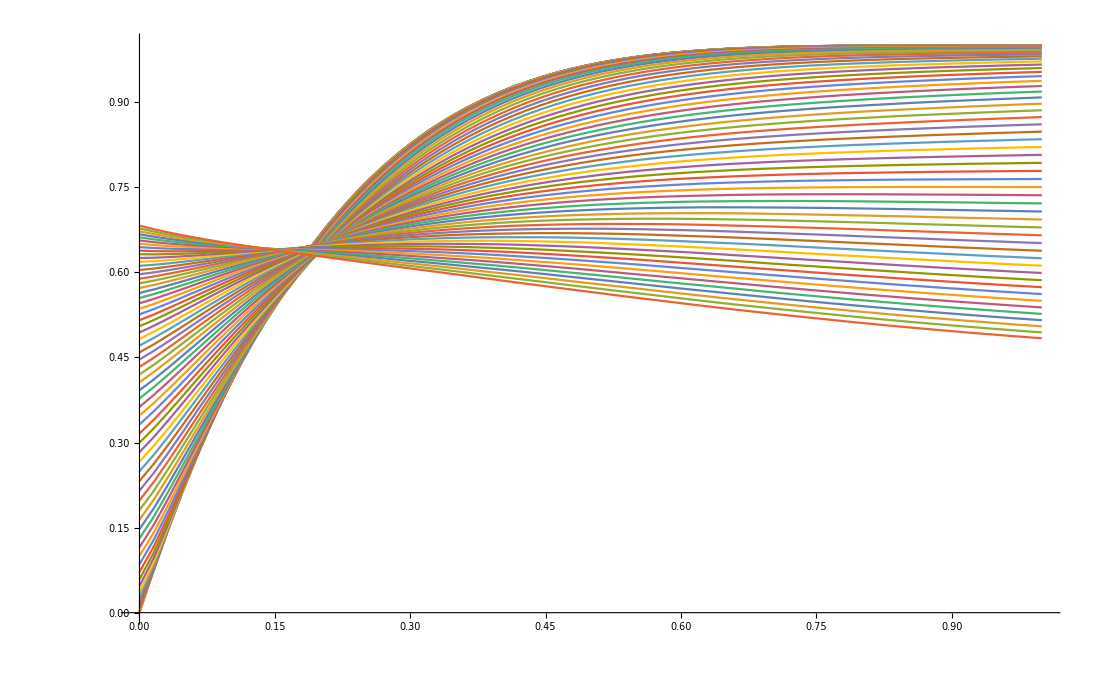

```mathematica
curvesA=Table[Table[{(NdV-1)/63,rawBRDFpart[[1+64*(Roughness-1)+(NdV-1)]][[1]]},{NdV,1,64}],{Roughness,1,64,1}];
ListLinePlot[curvesA,PlotRange->All]
```

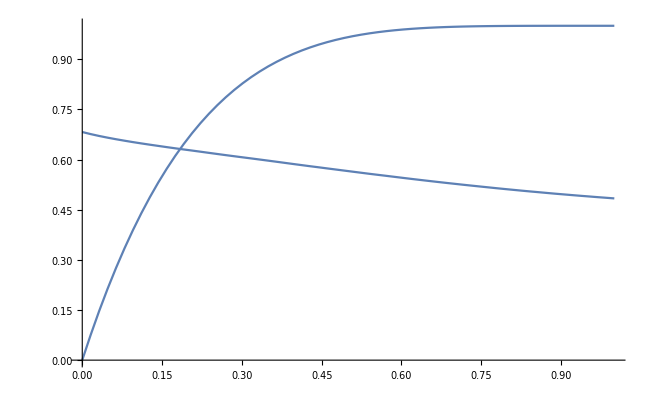

```mathematica
Show[ListLinePlot[curvesA[[1]],PlotRange->All],ListLinePlot[curvesA[[64]],PlotRange->All]]
```

{a→1.14377,b→-1.49442,c→-4.73489,d→-0.258065,e→-0.142441}

Function[x,1.14377-1.49442 ⅇ^(-0.258065-4.73489 x)-0.142441 x]

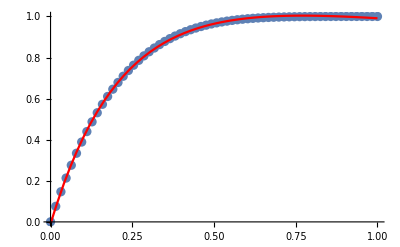

```mathematica
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";
fittingMethod="LevenbergMarquardt";


Clear[a,b,c,d,e]
(*modelOriginB=Exp[-a*Sin[c*x]^b];*)
modelA=a+b*x+c*x^2;
modelA=a+b*x+c*x^2+d*x^3;
modelA=a+b*x+c*x^2+d*x^3+e*x^4;
modelA=a+b*Exp[c*(d-x)];
modelA=a+b*Exp[c*x+d]+e*x;
fittingA = FindFit[curvesA[[1]],modelA,{{a,1},{b,-1},{c,-1},{d,0},e},x,Method->fittingMethod]
functionA =Function[x,Evaluate[ modelA/.fittingA]]
Show[
ListPlot[curvesA[[1]]],
Plot[functionA[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

```mathematica
curvesA[[1]][[1]][[2]];
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit :: cvmit will be suppressed during this calculation.

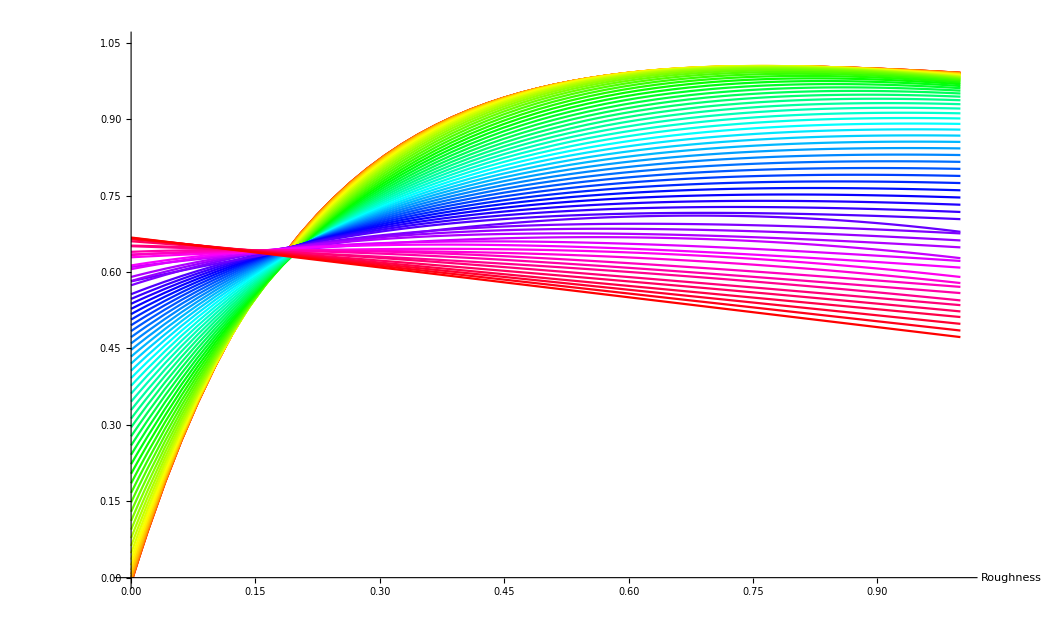

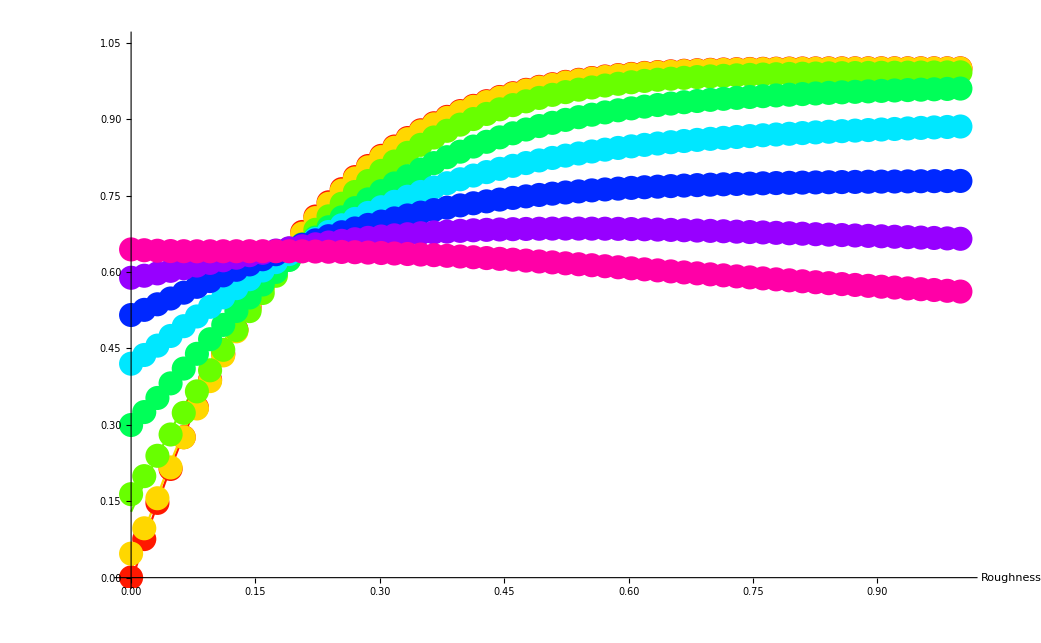

```mathematica
fittingA = Table[FindFit[ curvesA[[j]],modelA,{{a,1},{b,-1},{c,-1},{d,0},e},x ,Method->fittingMethod],{j,1,64}];
MatrixForm[fittingA];
MatrixForm[modelA/.fittingA];
Show[
Table[Plot[modelA/.fittingA[[j]],{x,0,1.0},PlotRange->{0,1.05},PlotStyle->Hue[j/64],AxesLabel->{"Roughness",}],{j,1,64}]]
Show[
Table[Plot[modelA/.fittingA[[j]],{x,0,1.0},PlotRange->{0,1.05},PlotStyle->Hue[j/64],AxesLabel->{"Roughness",}],{j,1,64,8}],
Table[ListPlot[curvesA[[j]],PlotRange->{0,1.0} ,PlotStyle->Hue[j/64],AxesLabel->{"Roughness",}],{j,1,64,8}]
]
```

### Representing & Fitting Individual Parameters

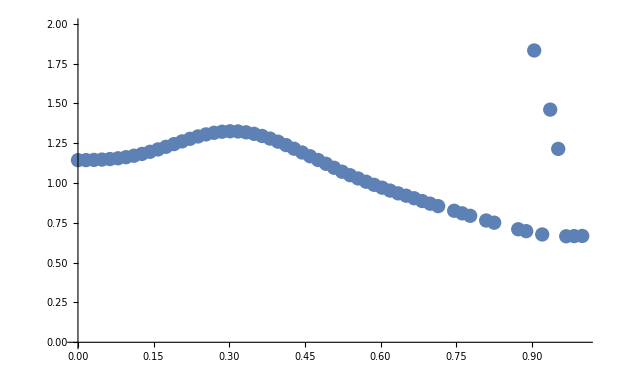

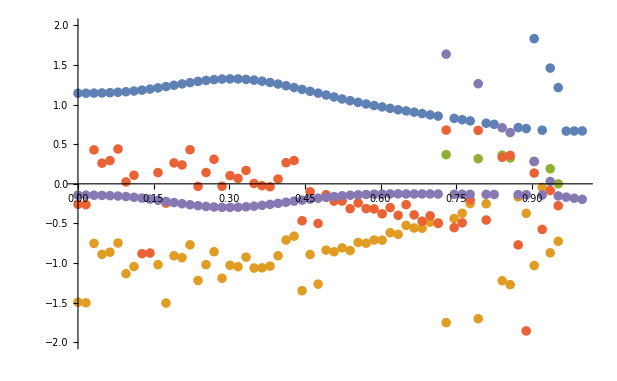

```mathematica
curvesAa = Table[{(i-1)/63, a/.fittingA[[i]]},{i,1,64}];
curvesAb = Table[{(i-1)/63, b/.fittingA[[i]]},{i,1,64}];curvesAc = Table[{(i-1)/63, c/.fittingA[[i]]},{i,1,64}];curvesAd = Table[{(i-1)/63, d/.fittingA[[i]]},{i,1,64}];
curvesAe = Table[{(i-1)/63, e/.fittingA[[i]]},{i,1,64}];(*curvesBf = Table[{(i-1)/63, f/.fittingCurvesB[[i]]},{i,1,64}];ListPlot[{curvesBa,curvesBb,curvesBc,curvesBd,curvesBe,curvesBf}]*)
ListPlot[curvesAa]
ListPlot[{curvesAa,curvesAb,curvesAc,curvesAd,curvesAe},PlotRange->{-2,2}]
```

#### Now fitting a,b,c,d,e

Now that we know the behavior of coefficients a, b, c, d & e depending on roughness, we can try and fit them too!

```mathematica
fittingMethod="PrincipalAxis";
fittingMethod="InteriorPoint";
fittingMethod="ConjugateGradient";
fittingMethod="LevenbergMarquardt";
fittingMethod="QuasiNewton";
fittingMethod="Newton";
fittingMethod="Automatic";

generalModelCoeffs = a+b*x+c*x^2+d*x^3+e*x^4+f*x^5;
generalModelCoeffs = a+b*x+c*x^2+d*x^3;
generalModelCoeffs = a+b*x;
(*generalModelCoeffs = a+b*x+c*Exp[d*x]*Cos[e*x];*)

(* Use modelOriginB function for our initial parameter a *)
(*generalModelCoeffs = Evaluate[modelOriginB[x]]+b*x+c*x^2+d*x^3+e*x^4+f*x^5*)
```

Function[x,1.2-0.5 x]

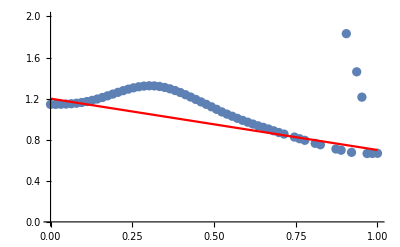

```mathematica
modelCoeffA=a+b*x;
fittingCoeffA = FindFit[Table[curvesAa[[i]],{i,1,32}],modelCoeffA,{{a,1},{b,-1},{c,0.1},{d,-1},e,f},x,Method->fittingMethod];

fittingCoeffA = {a-> 1.2, b-> (0.70-1.2)};
modelCoeffA = Function[x,Evaluate[modelCoeffA/.fittingCoeffA]]
Show[
ListPlot[Table[curvesAa[[i]],{i,1,64}],PlotRange->{{0,1},{0,2}}],
Plot[modelCoeffA[x],{x,0,1},PlotStyle->Red]
]
```

#### Reducing the model knowing a’s expression

We know that modelA=a+b*x 
And a=1.2-0.5 x with x = roughness

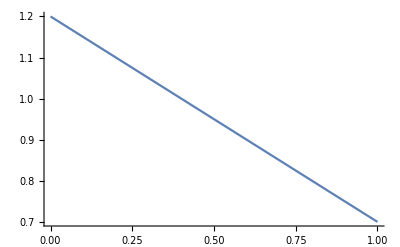

```mathematica
fA[α_]=1.2-0.5 α;
Plot[fA[x],{x,0,1}]
modelA2=fA[α]+b*Exp[c*x+d]+e*x;
```

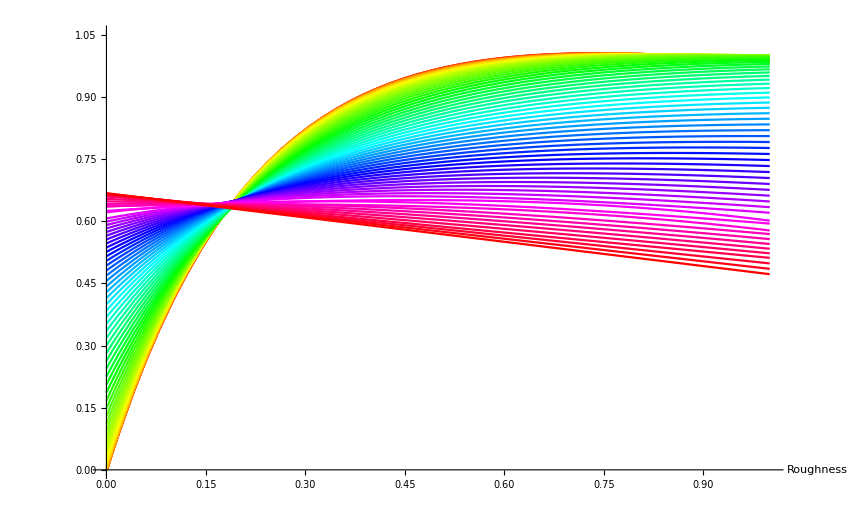

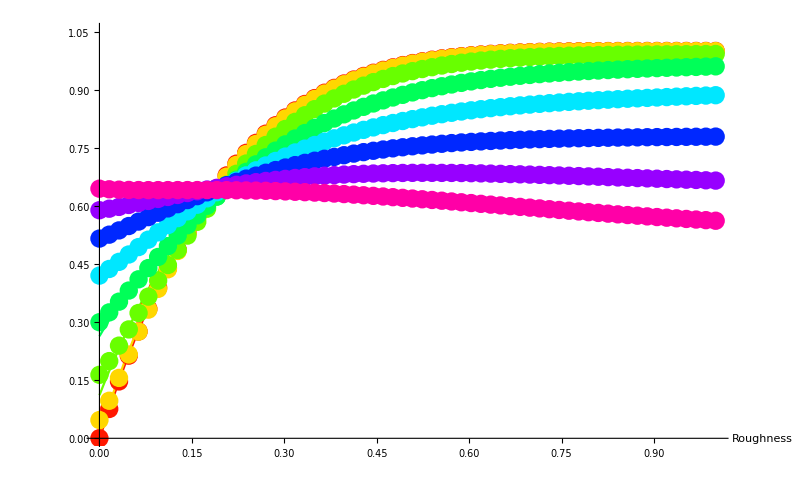

```mathematica
fittingA2 = Table[FindFit[ curvesA[[j]],modelA2/.α-> (j-1)/63,{{b,-1},{c,-1},{d,0},e},x ,Method->fittingMethod],{j,1,64}];
MatrixForm[fittingA2];
MatrixForm[modelA2/.fittingA2];
Show[
Table[Plot[modelA2/.α-> (j-1)/63/.fittingA2[[j]],{x,0,1.0},PlotRange->{0,1.05},PlotStyle->Hue[j/64],AxesLabel->{"Roughness",}],{j,1,64}]]
Show[
Table[Plot[modelA2/.α-> (j-1)/63/.fittingA2[[j]],{x,0,1.0},PlotRange->{0,1.05},PlotStyle->Hue[j/64],AxesLabel->{"Roughness",}],{j,1,64,8}],
Table[ListPlot[curvesA[[j]],PlotRange->{0,1.0} ,PlotStyle->Hue[j/64],AxesLabel->{"Roughness",}],{j,1,64,8}]
]
```

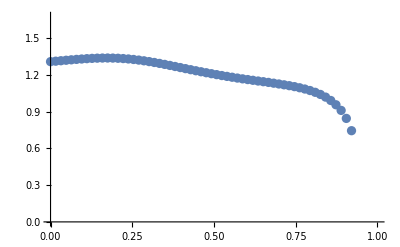

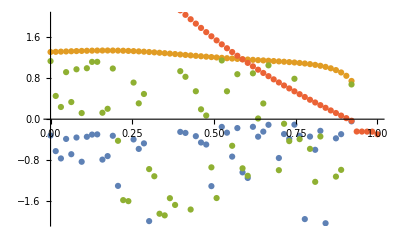

```mathematica
curvesAb = Table[{(i-1)/63, b/.fittingA2[[i]]/.α-> (i+1)/63},{i,1,64}];curvesAc = Table[{(i-1)/63, c/.fittingA2[[i]]/.α-> (i+1)/63},{i,1,64}];curvesAd = Table[{(i-1)/63, d/.fittingA2[[i]]/.α-> (i+1)/63},{i,1,64}];
curvesAe = Table[{(i-1)/63, e/.fittingA2[[i]]/.α-> (i+1)/63},{i,1,64}];
ListPlot[curvesAc]
ListPlot[{curvesAb,curvesAc,curvesAd,curvesAe},PlotRange->{-2,2}]
```

Function[x,1.35261-0.4 x]

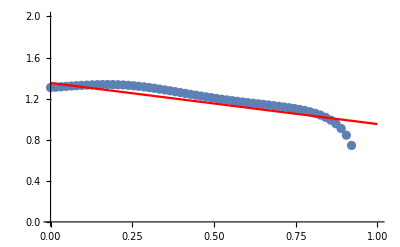

```mathematica
modelCoeffC=a+b*x;
fittingCoeffC = FindFit[Table[curvesAc[[i]],{i,1,32}],modelCoeffC,{{a,1},{b,-1},{c,0.1},{d,-1},e,f},x,Method->fittingMethod];
fittingCoeffC = {a-> 1.3526143638483663, b-> -0.4};
modelCoeffC = Function[x,Evaluate[modelCoeffC/.fittingCoeffC]]
Show[
ListPlot[Table[curvesAc[[i]],{i,1,64}],PlotRange->{{0,1},{0,2}}],
Plot[modelCoeffC[x],{x,0,1},PlotStyle->Red]
]
```

1.35261-0.4 α

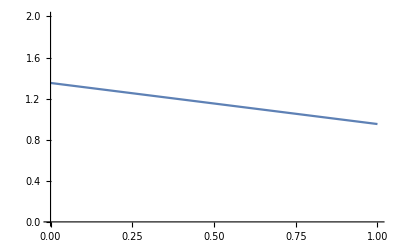

```mathematica
fC[α_]=a+b *α/.fittingCoeffC
Plot[fC[x],{x,0,1},PlotRange->{0,2}]
modelA3=fA[α]+b*Exp[fC[α]*x+d]+e*x;
```

```mathematica
fittingMethod="PrincipalAxis";
fittingMethod="InteriorPoint";
fittingMethod="ConjugateGradient";
fittingMethod="LevenbergMarquardt";
fittingMethod="QuasiNewton";
fittingMethod="Automatic";
fittingMethod="Newton";
```

FindFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindFit :: lstol will be suppressed during this calculation.

FindFit::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindFit :: sdprec will be suppressed during this calculation.

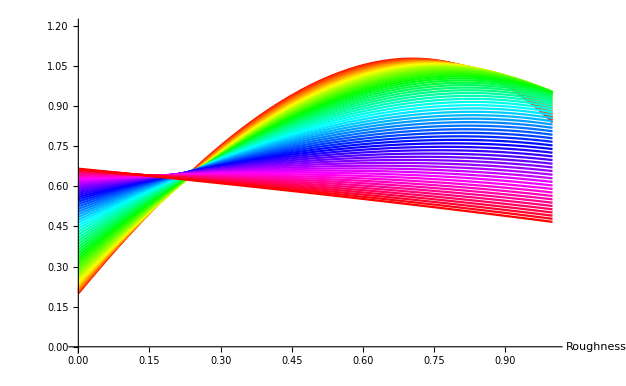

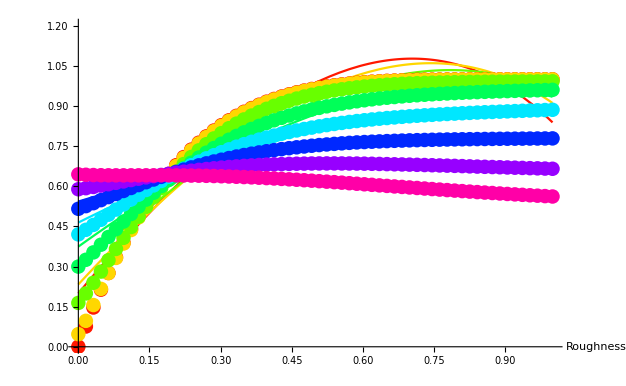

```mathematica
fittingA3 = Table[FindFit[ curvesA[[j]],modelA3/.α-> (j-1)/63,{{b,-1},{d,0},e},x ,Method->fittingMethod],{j,1,64}];
MatrixForm[fittingA3];
MatrixForm[modelA3/.fittingA3];
Show[
Table[Plot[modelA3/.α-> (j-1)/63/.fittingA3[[j]],{x,0,1.0},PlotRange->{0,1.2},PlotStyle->Hue[j/64],AxesLabel->{"Roughness",}],{j,1,64}]]
Show[
Table[Plot[modelA3/.α-> (j-1)/63/.fittingA3[[j]],{x,0,1.0},PlotRange->{0,1.2},PlotStyle->Hue[j/64],AxesLabel->{"Roughness",}],{j,1,64,8}],
Table[ListPlot[curvesA[[j]],PlotRange->{0,1.0} ,PlotStyle->Hue[j/64],AxesLabel->{"Roughness",}],{j,1,64,8}]
]
```

### Plotting the result & comparing with data

```mathematica
(*fitB[NdotV_,r_]:=modelCoeffA[r]+modelCoeffB[r]*NdotV+modelCoeffC[r]*NdotV^2+modelCoeffD[r]*NdotV^3;*)
(*fitB[NdotV_,r_]:=modelCoeffA[r]+modelCoeffB[r]*NdotV+modelCoeffC[r]*NdotV^2+modelCoeffD[r]*NdotV^3+modelCoeffE[r]*NdotV^4;*)

fitB[NdotV_,r_]:=modelCoeffA[r]*NdotV+modelCoeffB[r]*NdotV^2+modelCoeffC[r]*NdotV^3+modelCoeffD[r]*NdotV^4+modelCoeffE[r]*NdotV^5;

Show[Plot3D[fitB[NdotV,r],{NdotV,0,1},{r,0,1},PlotRange->{0,1},AxesLabel->{"N.V","Roughness"},PlotStyle->ColorData["RedBlueTones"]],
ListPlot3D[BRDFpartB,PlotRange->Full,AxesLabel->{"N.V","Roughness"}]]
```

-Graphics3D-

#### Test directly fitting a 3D function...

```mathematica
(*data=Table[{(Mod[i,64])/63,Floor[i/64] / 63,BRDFpartB[[1+Floor[i/64]]][[1+Floor[Mod[i,64]]]]},{i,0,128,1}];*)
data=BRDFpartB;
```

```mathematica
Clear[a,b,c,d,f,g]
ListPlot3D[data,PlotRange->{{0,1},{0,1},{0,1}},AxesLabel->{"x","y"}]

fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";

(*pipoModel =a+b*x+c*x^2 d*x^3+e*y+f*y^2+ g*x*y;*)
(*data=Table[{Mod[i,64]/63,Floor[i/64] / 63,BRDFpartB[[1+Floor[i/64]]][[1+Floor[Mod[i,64]]]]},{i,0,64*64-1,1}];*)

(* Exponential model
pipoModel =c*Exp[a*(x-x0)+b*(y-y0)];
pipoFit=FindFit[data,pipoModel,{{a,0},{b,1},{c,1},{d,1},e,{f,1},g,h,i,x0,y0,x1,y1},{x,y},Method->fittingMethod];
*)
(* Exp2 model *)
pipoModel =c*Power[2,a*(x-x0)+b*(y-y0)];
pipoFit=FindFit[data,pipoModel,{{a,1},{b,1},{c,1},{d,1},e,{f,1},g,h,i,x0,y0,x1,y1},{x,y},Method->fittingMethod];

pipoModel=Function[{x,y},Evaluate[pipoModel/.pipoFit]]
Plot3D[pipoModel[x,y],{x,0,1},{y,0,1},PlotRange->{{0,1},{0,1},{0,1.05}},AxesLabel->{"x","y"}]
Show[ListPlot3D[data,PlotRange->Full],Plot3D[pipoModel[x,y],{x,0,1},{y,0,1},PlotRange->Full,PlotStyle->Hue[0.58,0.5,0.67]]]
```

-Graphics3D-

Function[{x,y},0.00111328 2^(-8.14935 (-0.846665+x)-2.08142 (-1.46941+y))]

-Graphics3D-

-Graphics3D-

```mathematica
errAbs=Table[{data[[i]][[1]],data[[i]][[2]],100.0*Abs[data[[i]][[3]]-pipoModel[Mod[i-1,64]/63,Quotient[i-1,64]/63]]},{i,1,64*64}];
errRel=Table[{data[[i]][[1]],data[[i]][[2]],100.0*Abs[data[[i]][[3]]/pipoModel[Mod[i-1,64]/63,Quotient[i-1,64]/63]-1]},{i,1,64*64}];
ListPlot3D[errAbs,PlotRange->Full]
ListPlot3D[errRel,PlotRange->Full]
```

-Graphics3D-

-Graphics3D-

Fitting the F0-dependant curve

```mathematica
data=BRDFpartA;
```

```mathematica
Clear[a,b,c,d,f,g]
ListPlot3D[data,PlotRange->{{0,1},{0,1},{0,1.2}},AxesLabel->{"x","y"}]

fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";

(* Exp2 model *)
pipoModel =c*Exp[a*(x-x0)]*Exp[b*(y-y0)];
pipoFit=FindFit[data,pipoModel,{{a,1},{b,1},{c,0},{d,1},e,{f,1},g,h,i,x0,y0,x1,y1},{x,y},Method->fittingMethod];

(*pipoModel =a*Sin[b*(x-x0)]*Sin[c*(y-y0)];
pipoFit=FindFit[data,pipoModel,{{a,1},{b,1},{c,1},{d,1},e,{f,1},g,h,i,x0,y0,x1,y1},{x,y},Method->fittingMethod];
*)
pipoModel=Function[{x,y},Evaluate[pipoModel/.pipoFit]]
Plot3D[pipoModel[x,y],{x,0,1},{y,0,1},PlotRange->{{0,1},{0,1},{0,1.2}},AxesLabel->{"x","y"}]
Show[ListPlot3D[data,PlotRange->Full],Plot3D[pipoModel[x,y],{x,0,1},{y,0,1},PlotRange->Full,PlotStyle->Hue[0.58,0.5,0.67]]]
```

-Graphics3D-

Function[{x,y},0.890769 ⅇ^(0.498931 (-1.36478+x)-0.411362 (-1.04917+y))]

-Graphics3D-

-Graphics3D-

## Paraboloïd Shadow Mapping

```mathematica
Plot3D[{1-x^2-y^2,0},{x,-1,1},{y,-1,1}]
```

-Graphics3D-

### Using a sigmoïd to simulate the step function

```mathematica
sigmoid[x_,k_] := 1 / (1+Exp[-k*x]);
Manipulate[Plot[sigmoid[x,k], {x,-10, 10},PlotRange->Full], {{k,1},1/100,100}]
```

```mathematica
Series[sigmoid[x,10],{x,0,8}]
```

1/2+(5 x)/2-(125 x^3)/6+(625 x^5)/3-(265625 x^7)/126+O[x]^9

```mathematica
approx[x_]:=1/2+(5 x)/2-(125 x^3)/6+(625 x^5)/3-(265625 x^7)/126
```

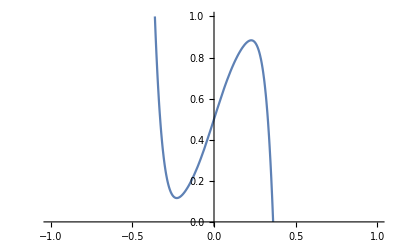

```mathematica
Plot[approx[x],{x,-1,1},PlotRange->{0,1}]
```

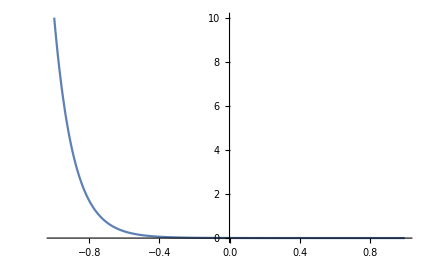

```mathematica
a = 1.0;
b =  0.1;
altitude = 100.0;
hitDistance = 100.0;
density[dy_]:= a  Exp[-b * altitude] (1 - Exp[-b * dy * hitDistance]) / (b * dy);
Plot[density[x], {x, -1.0, 1 }, PlotRange->Full]
```